```mathematica
Clear[Evaluate[Context[]<>"*"]]
```

This file extends the model of Gardner 2010 JTB to our setting. 

Assumptions : there is an infinite number of demes in the population, so that the probability of identity by descent of two individuals coming from different demes is 0.

The probability that two individuals from the same deme share the same parent, given that their parents come from the same patch, is denoted α. In the main text, we have α=1/n; here we assume that there can be reproductive bias, leading to α!=1/n.   

As in Gardner 2010, we are focusing on a Wright-Fisher life-cycle.

#### Recursion on Q (probabilities of identity by descent)

Two different adult individuals from the same deme are identical by descent (IBD) if
- either none of the offspring emigrated ((1-m)^2) nor is a mutant ((1-μ)^2), 
 and they have the same parent (α), who is IBD to itself, 
 or they have different parents (1-α), and the parents were IBD (Qin);
 - or immigration took place, and since we are considering the case of an infinite number of demes, then the parents were not IBD (Qout = 0 when the number of demes is infinite).

```mathematica
Solve[Qinαi==(1-μ)^2(1-m)^2(α* 1 + (1-α)*Qinαi), Qinαi]//FullSimplify
solQ = %⟦1⟧;
```

{{Qinαi→((-1+m)^2 α (-1+μ)^2)/(1+(-1+m)^2 (-1+α) (-1+μ)^2)}}

(and R = Qin in this case, since Qout = 0)

#### B and C

Values of B and C in the WF life - cycle (those are not affected by α and hence the same as in the main text)

```mathematica
CWF=(1-μ)c+(b-c)(1-μ)((1-m)^2/n+m^2/(n d-n));
BWF=(1-μ)b-(n-1)(b-c)(1-μ)((1-m)^2/n+m^2/(n d-n));
```

We consider the infinite deme versions (d->∞)

```mathematica
CWFi=Limit[CWF,d->∞]//FullSimplify
BWFi=Limit[BWF,d->∞]//FullSimplify
```

-(((b-c) (-1+m)^2+c n) (-1+μ))/n

((-b (-1+m)^2-c (-1+m)^2 (-1+n)+b (-2+m) m n) (-1+μ))/n

#### Measure of success : B R - C

Success when B R - C > 0

```mathematica
fit=BWFi (Qinαi/.solQ)-CWFi//FullSimplify
```

(((b-c) (-1+m)^2+c n+((-1+m)^2 (-b (-1+m)^2-c (-1+m)^2 (-1+n)+b (-2+m) m n) α (-1+μ)^2)/(1+(-1+m)^2 (-1+α) (-1+μ)^2)) (-1+μ))/n

Set parameters

```mathematica
prms={b->10,c->1,n->4};
```

Plot contour of B R - C == 0, i.e. threshold value of α above which altruists win over defectors

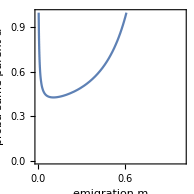

```mathematica
ContourPlot[(fit/.prms/.μ->0.01)==0,{m,0,1},{α,0,1},PlotRange-> {{0,1},{0,1},Automatic}, FrameLabel->{"emigration m", "proba same parent α"}]
```

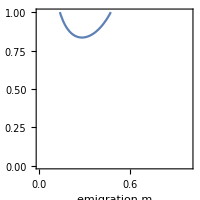

```mathematica
ContourPlot[(fit/.prms/.μ->0.15)==0,{m,0,1},{α,0,1},PlotRange-> {{0,1},{0,1},Automatic}, FrameLabel->{"emigration m", "proba same parent α"}]
```

Find critical value of α

```mathematica
αsol=Solve[fit==0,α]//FullSimplify
αcrit=α/.αsol⟦1⟧;
```

{{α→(((b-c) (-1+m)^2+c n) (m (-1+μ)-μ) (2+m (-1+μ)-μ))/((b-c) (-2+m) (-1+m)^2 m n (-1+μ)^2)}}

C format to copy in R for plotting

```mathematica
CForm[αcrit/.μ->mutation]
```

((m*(-1 + mutation) - mutation)*(2 + m*(-1 + mutation) - mutation)*
     ((b - c)*Power(-1 + m,2) + c*n))/
   ((b - c)*(-2 + m)*Power(-1 + m,2)*m*Power(-1 + mutation,2)*n)

Compare μ = 0 and low migration limit
(again issues with the orders of limits)

```mathematica
Limit[Limit[αcrit, μ->0],m->0]//FullSimplify
Limit[Limit[αcrit, m->0],μ->0]//FullSimplify
```

c/(b-c)+1/n

DirectedInfinity[b-c+c n]/(b n-c n)

Slope of α wrt m (m->0)

```mathematica
dα=D[αcrit,m]//FullSimplify
dα0=Limit[dα,m->0]//FullSimplify
```

(-2 c (-2+m)^2 m^2 n+4 (-1+m)^4 (b+c (-1+n)) μ-2 (-1+m)^4 (b+c (-1+n)) μ^2)/((b-c) (-2+m)^2 (-1+m)^3 m^2 n (-1+μ)^2)

DirectedInfinity[(b+c (-1+n)) (-2+μ) μ]/((b-c) n (-1+μ)^2)

-> the slope is negative except when μ =0